```mathematica
testScale[graphic_] := Module[{imageSizeInPoints,scale},
imageSizeInPoints=20*28.35;
scale=Show[graphic,Graphics[{Thick,Black,Line[{{1,1},{2,1}}]}],Axes->True,PlotRange->{{-10,10},{0,29}}];
Export["graphic.pdf",scale,ImageSize->imageSizeInPoints];
scale
]
```

```mathematica
arena=<|
"Type"->"Cone",
"DiskRadius"->1.25,
"ConeSemiAngle"->π/8,
"zRange"->{0,30}
|>;
arena=Append[arena,"IDmax"->100];
run=doParameterisedRun[arena];
```

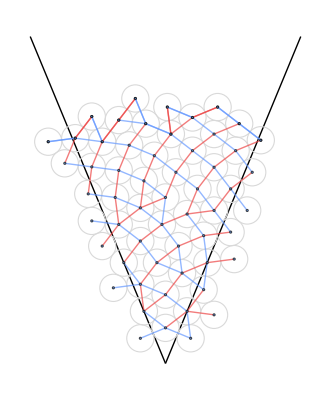

```mathematica
displayRun[run]
```

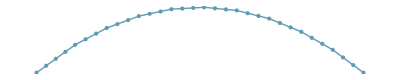

```mathematica
displayPrintCone[arena]
```

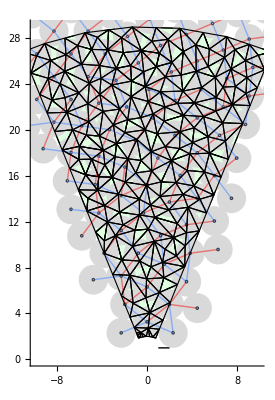

```mathematica
displayPrintCone[arena_] := Module[{zLimit,xLimit},
zLimit=29;
xLimit=zLimit Tan[arena["ConeSemiAngle"]];
DiscretizeRegion@RegionDifference[
Disk[{0,0},zLimit,π/2+{-arena["ConeSemiAngle"],arena["ConeSemiAngle"]}],
Disk[{0,0},2]]
];
displayPrintConeBoundary[arena_] := Module[{zLimit,xLimit},
zLimit=29;
xLimit=zLimit Tan[arena["ConeSemiAngle"]];
DiscretizeRegion@RegionBoundary@RegionDifference[
Disk[{0,0},zLimit,π/2+{-arena["ConeSemiAngle"],arena["ConeSemiAngle"]}],
Disk[{0,0},2]]


];
testScale[printRun[run]]
```

```mathematica
printRun[run_]:=Module[{labels,diskGraph,chainGraph,arena},
disks=#Disk&/@ run["Logging"]["Disks"];
chainGraph=makeChainGraph[run];
arena=run["Arena"];
Show[
Graphics[{FaceForm[LightGray],EdgeForm[None],
displayPrintCone[arena]}],
Graphics
[{
{FaceForm[White],EdgeForm[None],Values[disks]}
(*displayDiskNumbers[arena,disks,Keys[disks]]
*)}],
makeGraph[run],
Graphics[{FaceForm[None],EdgeForm[Black],
displayPrintConeBoundary[arena]}]
]
]
```

```mathematica
region
```

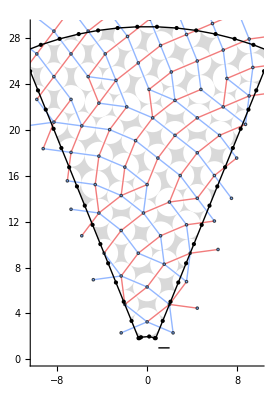

```mathematica
testScale[printRun[run]]
```